## Primera Parte: Carga inicial de los datos enpecyt2013_cb1.dbf

```mathematica
datacb1 = Import["/Users/guillemontanari/C3/Datos/ENPECyT/2013/enpecyt2013_bd/enpecyt2013_cb1.dbf", "LabeledData"];
```

```mathematica
(* Ver cantidad de columnas / varia en la DB *)
Length[datacb1]
```

245

```mathematica
PositionIndex[datacb1[[All,1]]];
```

```mathematica
(* S3P1 - columna 8 - es el nivel de instruccion: de 0 a 10 *)
Length[datacb1[[8,2]]]
```

2857

```mathematica
(* S4P10 - columna 8 - es el acceso a internet 1 Si - 2 No - Null *)
Length[datacb1[[99,2]]]
```

2857

```mathematica
(* FAC - columna 245 - es el nivel de instruccion: de 0 a 10 *)
Total[datacb1[[-1,2]]]
```

34818927

## Segunda Parte: Análisis exploratorio

```mathematica
(*Datos 
1 - Nivel de Instruccion Pos 8
2 - Acceso a internet Pos 99 ( 1= SI, 2 = No, NULL ???
Teniendo en cuenta los Factores de expansión Pos 245 *)
```

## Nivel de Instrucción

```mathematica
instruccion = datacb1[[8,2]];
```

```mathematica
factores = datacb1[[-1,2]];
```

```mathematica
datainst= Transpose[{factores, instruccion}];
```

```mathematica
ginstrdata = GatherBy[datainst, #[[2]] & ];
```

```mathematica
datosinstr= ToExpression[Sort[Map[{#[[1,2]],Total[#[[All,1]]] }& ,ginstrdata]]]
```

{{0,1032489},{1,41016},{2,6560125},{3,8228730},{4,6593799},{5,410701},{6,2634016},{7,8194738},{8,297681},{9,694527},{10,131105}}

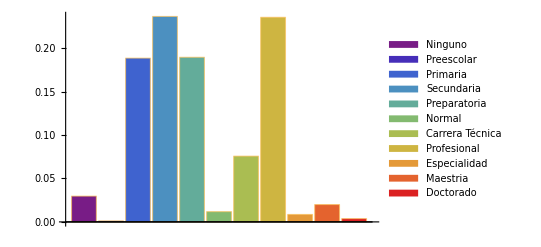

```mathematica
BarChart[N[datosinstr[[All,2]]/34818927],ChartStyle->"Rainbow",
ChartLegends->{"Ninguno","Preescolar","Primaria","Secundaria","Preparatoria","Normal","Carrera Técnica","Profesional","Especialidad", "Maestria","Doctorado"}]
```

## Acceso a Internet

```mathematica
internet = datacb1[[99,2]];
```

```mathematica
dataninter = Transpose[{factores, internet}];
```

```mathematica
ginterdata = GatherBy[dataninter, #[[2]] & ];
```

```mathematica
inter =Sort[ToExpression[Map[{#[[1,2]],Total[#[[All,1]]] }& ,ginterdata]]];
```

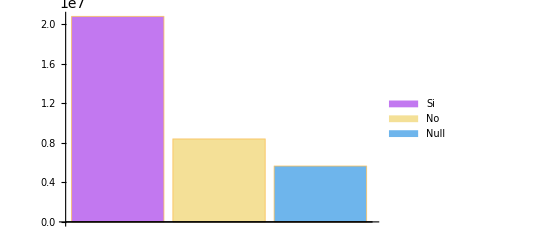

```mathematica
BarChart[inter[[All,2]],ChartStyle->"Pastel",ChartLegends->{"Si","No","Null"}]
```

## Primera Parte: Carga inicial de los datos enpecyt2013_cs.dbf

```mathematica
datacs = Import["/Users/guillemontanari/C3/Datos/ENPECyT/2013/enpecyt2013_bd/enpecyt2013_cs.dbf", "LabeledData"];
```

```mathematica
Length[datacs]
```

23

```mathematica
PositionIndex[datacs[[All,1]]];
```

```mathematica
datacs[[{10, 11,15,23},1]]
```

{SEX,EDA,NIV,FAC18}

```mathematica
Length[datacs[[23,2]]]
```

10418

```mathematica
Total[datacs[[-1,2]]]
```

34818927

## Segunda Parte: Análisis inicial de los datos Sexo

```mathematica
sexo= datacs[[10,2]];
```

```mathematica
factores2 = datacs[[-1,2]];
```

```mathematica
datan2 = Transpose[{factores2, sexo}];
```

```mathematica
gdatacs = GatherBy[datan2, #[[2]] & ];
```

```mathematica
datos2 = Map[Total[#[[All,1]]] & ,gdatacs]
```

{18644082,16174845}

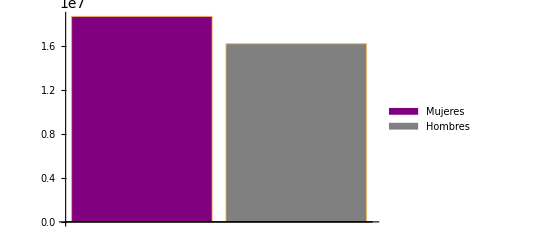

```mathematica
BarChart[datos2,ChartStyle->{Purple,Gray},ChartLegends->{"Mujeres", "Hombres"}]
```

## Edad

```mathematica
edad = datacs[[11,2]];
```

```mathematica
edata = Transpose[{factores2, edad}]
```

{{0,067},{0,054},{0,059},{0,009},{0,011},{14315,032},{0,030},{0,062},{0,004},{0,005},{4772,027},{9543,071},{0,061},10392,{0,017},{0,038},{8970,050},{0,008},{0,011},{0,017},{4485,055},{0,010},{0,001},{0,052},{0,016},{8970,021},{4503,041}}
 |  |  |  |

```mathematica
Quotient[ToExpression[edata[[-1,2]]],10]
```

4

```mathematica
edadf= GatherBy[edata,Quotient[ToExpression[#[[2]]],10]&];
```

```mathematica
Length[edadf]
```

11

```mathematica
tedad= Sort[Map[{Quotient[ToExpression[#[[1,2]]],10],Total[#[[All,1]]]}&,edadf]]
```

{{0,0},{1,1844188},{2,8258189},{3,7585995},{4,7007222},{5,5122807},{6,3029809},{7,1416874},{8,520109},{9,33734},{10,0}}

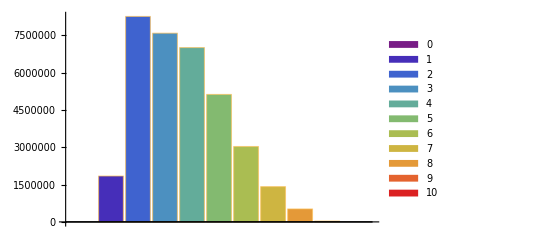

```mathematica
BarChart[tedad[[All,2]], ChartStyle->"Rainbow", ChartLegends->{tedad[[All,1]]}]
```

## Primera Parte : Carga inicial de los datos cb2.csv

```mathematica
datacb2 = Import["/Users/guillemontanari/C3/Datos/ENPECyT/2013/enpecyt2013_bd/cb2.csv", "CSV", "Numeric" -> False];
```

```mathematica
Length[datacb2]
```

2858

```mathematica
PositionIndex[datacb2[[1,All]]];
```

```mathematica
Total[ToExpression[datacb2[[2;;-1,-1]]]]
```

34818927

## Tercera Parte: Análisis conjunto

## 1. Armado de los indices

### tabla cs

```mathematica
datacs // Length
```

23

```mathematica
datacs[[All,1]];
```

```mathematica
tdatacs = Transpose[datacs[[1;;7,2]]];
```

```mathematica
tdatacs[[1]]; (* respuesta de la persona 1 *)
```

```mathematica
(* Busco el tipo de cada variable de esa lista para corroborar que son todas cadenas *)
Map[Head[#]&,tdatacs[[1]]];
```

```mathematica
(* Utilizo una funcion para juntar esta lista en una sola cadena para armar la clave o identificador único *)
StringJoin[tdatacs[[1]]];
```

```mathematica
stdatacs = Map[StringJoin[#] &,tdatacs];
```

```mathematica
stdatacs[[1]]
```

14081301400075102

```mathematica
stdatacs // Length
```

10418

```mathematica
(* Para verificar que sea unica, donde el resultado me dice que tengo 10418 1, entonces son unicas, porque no se repiten, sino el primer Tally me las hubiera agrupado juntas *)
Tally[Tally[stdatacs][[All,2]]]
```

{{1,10418}}

### tabla cb1

```mathematica
datacb1 // Length
```

245

```mathematica
datacb1[[All,1]];
```

```mathematica
tdatacbl = Transpose[datacb1[[1;;7,2]]];
```

```mathematica
tdatacbl[[1]];
```

```mathematica
Map[Head[#]&, tdatacbl[[1]]];
```

```mathematica
StringJoin[tdatacbl[[1]]];
```

```mathematica
stdatacbl = Map[StringJoin[#] &,tdatacbl];
```

```mathematica
stdatacbl[[1]]
```

14081301400072201

```mathematica
stdatacbl // Length
```

2857

```mathematica
Tally[Tally[stdatacbl][[All,2]]]
```

{{1,2857}}

### tabla cb2

```mathematica
datacb2 // Length
```

2858

```mathematica
tdatacb2 = datacb2[[2;;-1,1;;7]]
```

{{14,0813,01,40007,2,2,01},{14,0813,01,40007,5,1,05},{14,0813,01,40007,2,1,03},{14,0813,01,40007,3,1,01},{14,0813,01,40007,4,1,03},{14,0813,01,40007,1,1,02},2845,{32,0813,32,40364,2,1,01},{32,0813,32,40364,1,1,02},{32,0813,32,40396,4,1,02},{32,0813,32,40396,2,1,01},{32,0813,32,40396,3,1,01},{32,0813,32,40396,1,1,01}}
 |  |  |  |

```mathematica
tdatacb2[[1]];
```

```mathematica
Map[Head[#]&,tdatacb2[[1]]];
```

```mathematica
StringJoin[tdatacb2[[1]]];
```

```mathematica
stdatacb2 = Map[StringJoin[#] &,tdatacb2];
```

```mathematica
stdatacb2[[1]]
```

14081301400072201

```mathematica
stdatacb2 // Length
```

2857

```mathematica
Tally[Tally[stdatacb2][[All,2]]]
```

{{1,2857}}

## 2. Buscar de cada archivo las variables que nos interesan

### CS

```mathematica
(*Busco en datacs Sexo, Edad, Factor de expansion *)
vdatacs = Transpose[datacs[[{10,11,-2},2]]];
```

```mathematica
rdatacs = Range[Length[stdatacs]];
```

```mathematica
Map[stdatacs[[#]] -> vdatacs[[#]]&,rdatacs];
```

```mathematica
asocs = Association[Map[stdatacs[[#]] -> vdatacs[[#]]&,rdatacs]];
```

```mathematica
asocs["32081332403961101"]
```

{1,050,4495}

### CB1

```mathematica
(* Busco datos en DB cbl *)
vdatacbl = Transpose[datacb1[[{8,20,35,36,37,38,39,40,78,79,80,100,-2},2]]];
```

```mathematica
rdatacbl = Range[Length[stdatacbl]];
```

```mathematica
Map[stdatacbl[[#]] -> vdatacbl[[#]]&,rdatacbl];
```

```mathematica
asocbl = Association[Map[stdatacbl[[#]] -> vdatacbl[[#]]&,rdatacbl]];
```

```mathematica
asocbl["32081332403961101"]
```

{03,,2,2,2,2,2,2,007,000,001,2,1}

### CB2

```mathematica
vdatacb2 = datacb2[[2;;-1, {10,11,12}]];
```

```mathematica
rdatacb2 = Range[Length[stdatacb2]];
```

```mathematica
asocb2 = Association[Map[stdatacb2[[#]] -> vdatacb2[[#]]&,rdatacb2]];
```

```mathematica
asocb2["32081332403961101"]
```

{2,2,2}